# Lagaris Problem 5: 2nd-Order PDE BVP with Dirichlet BC

Solving the PDE in Mathematica:

```mathematica
pde=D[ψ[x,y],{x,2}]+D[ψ[x,y],{y,2}]==ⅇ^-x(x-2+y^3+6y)
```

ψ^(0,2)[x,y]+ψ^(2,0)[x,y]==ⅇ^-x (-2+x+6 y+y^3)

```mathematica
DSolve[{
pde,
ψ[0,y]==y^3,
ψ[1,y]==(1+y^3)/ⅇ,
ψ[x,0]==x ⅇ^-x,
ψ[x,1]==ⅇ^-x(x+1)
},ψ[x,y],{x,y}]
```

DSolve[{ψ^(0,2)[x,y]+ψ^(2,0)[x,y]==ⅇ^-x (-2+x+6 y+y^3),ψ[0,y]==y^3,ψ[1,y]==(1+y^3)/ⅇ,ψ[x,0]==ⅇ^-x x,ψ[x,1]==ⅇ^-x (1+x)},ψ[x,y],{x,y}]

```mathematica
ψa[x_,y_]:=ⅇ^-x(x+y^3)
```

```mathematica
FullSimplify[D[ψa[x,y],x]]
```

-ⅇ^-x (-1+x+y^3)

```mathematica
dψadx[x_,y_]:=-ⅇ^-x (-1+x+y^3)
```

```mathematica
FullSimplify[D[ψa[x,y],y]]
```

3 ⅇ^-x y^2

```mathematica
dψady[x_,y_]:=3 ⅇ^-x y^2
```

```mathematica
FullSimplify[D[ψa[x,y],{x,2}]]
```

ⅇ^-x (-2+x+y^3)

```mathematica
d2ψadx2[x_,y_]:=ⅇ^-x (-2+x+y^3)
```

```mathematica
FullSimplify[D[ψa[x,y],x,y]]
```

-3 ⅇ^-x y^2

```mathematica
d2ψadxdy[x_,y_]:=-3 ⅇ^-x y^2
```

```mathematica
FullSimplify[D[ψa[x,y],y,x]]
```

-3 ⅇ^-x y^2

```mathematica
d2ψadydx[x_,y_]:=-3 ⅇ^-x y^2
```

```mathematica
FullSimplify[D[ψa[x,y],{y,2}]]
```

6 ⅇ^-x y

```mathematica
d2ψady2[x_,y_]:=6 ⅇ^-x y
```

```mathematica
Plot3D[ψa[x,y],{x,0,1},{y,0,1},PlotLabel->"Problem 5 analytical solution (compare to Lagaris (1998), Figure 8)"]
```

-Graphics3D-

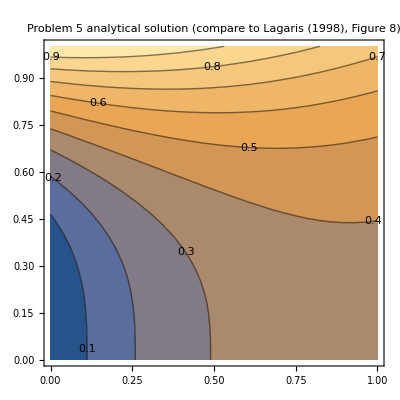

```mathematica
ContourPlot[ψa[x,y],{x,0,1},{y,0,1},PlotLabel->"Problem 5 analytical solution (compare to Lagaris (1998), Figure 8)",ContourLabels->True]
```

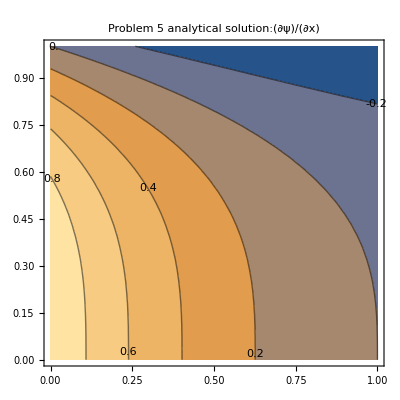

```mathematica
ContourPlot[dψadx[x,y],{x,0,1},{y,0,1},PlotLabel->"Problem 5 analytical solution:(∂ψ)/(∂x)",ContourLabels->True]
```

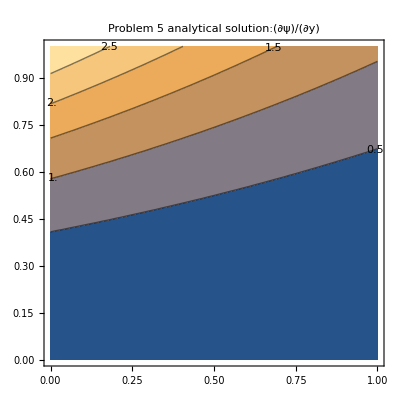

```mathematica
ContourPlot[dψady[x,y],{x,0,1},{y,0,1},PlotLabel->"Problem 5 analytical solution:(∂ψ)/(∂y)",ContourLabels->True]
```

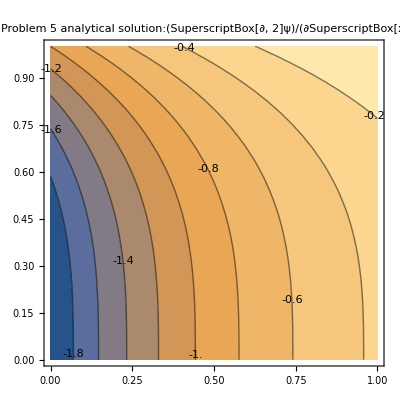

```mathematica
ContourPlot[d2ψadx2[x,y],{x,0,1},{y,0,1},PlotLabel->"Problem 5 analytical solution:(SuperscriptBox[∂, 2]ψ)/(∂SuperscriptBox[x, 2])",ContourLabels->True]
```

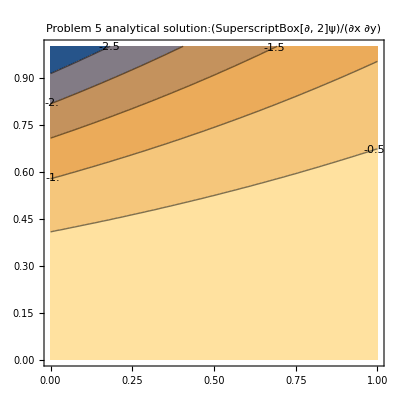

```mathematica
ContourPlot[d2ψadxdy[x,y],{x,0,1},{y,0,1},PlotLabel->"Problem 5 analytical solution:(SuperscriptBox[∂, 2]ψ)/(∂x ∂y)",ContourLabels->True]
```

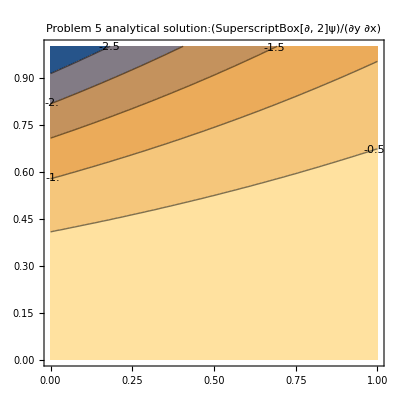

```mathematica
ContourPlot[d2ψadydx[x,y],{x,0,1},{y,0,1},PlotLabel->"Problem 5 analytical solution:(SuperscriptBox[∂, 2]ψ)/(∂y ∂x)",ContourLabels->True]
```

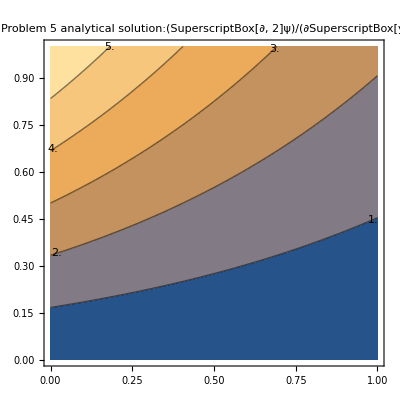

```mathematica
ContourPlot[d2ψady2[x,y],{x,0,1},{y,0,1},PlotLabel->"Problem 5 analytical solution:(SuperscriptBox[∂, 2]ψ)/(∂SuperscriptBox[y, 2])",ContourLabels->True]
```